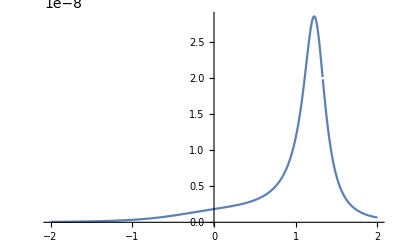

```mathematica
MHz=10^6;
Γ1=5.3*2π MHz;
Γ2=15.1*2π MHz;
Γ=Γ1+Γ2;
a=2.5*Γ1;
Ω=a (*(Γ1+Γ2)*);
Δ1=10* 2*π MHz;
Ωtilde=√(Abs[Ω]^2+Δ1^2);
ΔS=-Δ1/2+Sign[Δ1]/(2 √2)√(Ωtilde^2-Γ^2/4+√((Ωtilde^2-Γ^2/4)^2+Δ1^2 Γ^2));
κ=Γ ΔS/(Δ1+2ΔS);
S0[Δ2_]=(Abs[Ω]^2/4 Γ/(2 π))/Abs[(Δ2-Δ1-ΔS+ⅈ κ/2)(Δ2+ΔS+ⅈ (Γ-κ)/2)]^2;
Plot[S0[ 2π x ],{x,-20 MHz,20MHz},PlotRange->All]
(*Plot[FourierTransform[Sqrt[S0[2π x ]],x,t],{t,-1*10^-6,1*10^-6},PlotRange->All]
*)
```

```mathematica
(6.530147895335609*^7-7.713310580204779*^7)/2/π*2
```

-3.76612×10^6

```mathematica
{{6.530147895335609*^7,1.4450405207463747*^-8}}
```

-3.18544×10^6

```mathematica
1.6927374301675983*^7-1.8000000000000007*^7
```

-1.07263×10^6

```mathematica
Ωtildex=√(Abs[Ωx]^2+Δ1x^2);
ΔSx=-Δ1x/2+Sign[Δ1x]/(2 √2)√(Ωtildex^2-Γx^2/4+√((Ωtildex^2-Γx^2/4)^2+Δ1x^2 Γx^2));
κx=Γx ΔSx/(Δ1x+2ΔSx);
```

0

```mathematica
Limit[κx,Δ1x->0]
Limit[ΔSx,Δ1x->0]
Limit[ΔSx,Ωx->0]
```

Γx/2

(√(-Γx^2+4 Abs[Ωx]^2+√((Γx^2-4 Abs[Ωx]^2)^2)))/(4 √2)

-Δ1x/2+(√(-Γx^2/4+Δ1x^2+√(Γx^2 Δ1x^2+(-Γx^2/4+Δ1x^2)^2)) Sign[Δ1x])/(2 √2)

```mathematica
Limit[(Abs[Ωx]^2/4 Γx/(2 π))/Abs[(Δ2-Δ1x-ΔSx+ⅈ κx/2)(Δ2+ΔSx+ⅈ (Γx-κx)/2)]^2,Δ1x->0]
```

(8 Γx Abs[Ωx]^2)/(π Abs[Abs[Ωx]^2+1/4 (Γx^2-16 ⅈ Γx Δ2-32 Δ2^2+√((Γx^2-4 Abs[Ωx]^2)^2))]^2)

```mathematica
(Γx Abs[Ωx]^2)/(8 π Abs[(ⅈ Γx Δ2)/2+Δ2^2-Abs[Ωx]^2/8+1/128 Γx^2 (-8+√((Γx^2-4 Abs[Ωx]^2)^2))]^2)/.Ωx->0
```

0

```mathematica
Limit[Sign[x],x->0,Direction->1]
Limit[HeavisideTheta[x],x->0]
```

-1

1

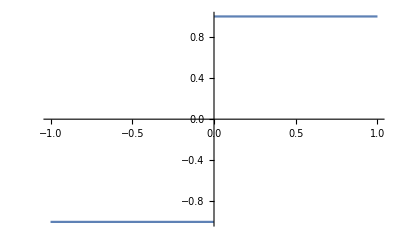

```mathematica
Plot[Sign[x],{x,-1,1}]
```

```mathematica
D[ΔSx,Ωx]//FullSimplify
```

(Abs[Ωx] √(-Γx^2+4 Δ1x^2+4 √(Γx^2 Δ1x^2+(-Γx^2/4+Δ1x^2+Abs[Ωx]^2)^2)+4 Ωx Conjugate[Ωx]) Sign[Δ1x] Abs'[Ωx])/(4 √2 √(Γx^2 Δ1x^2+(-Γx^2/4+Δ1x^2+Abs[Ωx]^2)^2))

```mathematica
(Abs[Ωx] √(-Γx^2+4 Δ1x^2+4 √(Γx^2 Δ1x^2+(-Γx^2/4+Δ1x^2+Abs[Ωx]^2)^2)+4 Ωx Conjugate[Ωx]) Sign[Δ1x] Abs'[Ωx])/(4 √2 √(Γx^2 Δ1x^2+(-Γx^2/4+Δ1x^2+Abs[Ωx]^2)^2))/.Ωx->0
```

0

```mathematica
FourierTransform[√S0[Δ2],Δ2,t]
```

FourierTransform[(2.89464×10^10)/Abs[((-1.51461×10^7+612210. ⅈ)+Δ2) ((146079.+6.34763×10^7 ⅈ)+Δ2)],Δ2,t]

```mathematica
dS=Table[√S0[Δ2],{Δ2,-600 MHz,600MHz,.1MHz}];
```

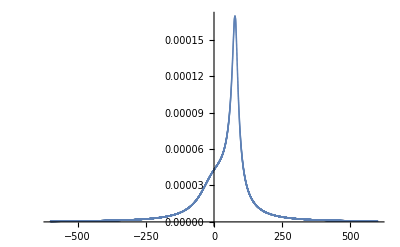

```mathematica
ListPlot[dS,PlotRange->All,DataRange->{-600,600}]
```